```mathematica
FullSimplify[ArcCurvature[{x,x^3-x},x],x∈Reals]
```

(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2))

```mathematica
Integrate[(6 Abs[x])/((2-6 x^2+9 x^4)^(3/2)),{x,-∞,∞}]
```

2+√2

```mathematica
N[2+√2]
```

3.41421

```mathematica
1/(√(1+x^2))
```

1/(√(1+x^2))

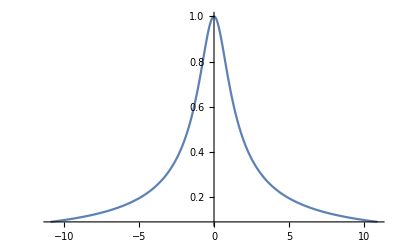

```mathematica
Plot[1/(√(1+x^2)),{x,-10.92,10.92}]
```

```mathematica
f[x_]:=1/(√(1+x^2))
```

```mathematica
FullSimplify[Normalize[{x,f[x]}].Normalize[{x,f[x]-a}],{x,a}∈Reals]
```

(1+x^2+x^4-a √(1+x^2))/(√((1+x^2) (1+x^2+x^4) (x^2+(a-1/(√(1+x^2)))^2)))

```mathematica
Manipulate[Plot[(1+x^2+x^4-a √(1+x^2))/(√((1+x^2) (1+x^2+x^4) (x^2+(a-1/(√(1+x^2)))^2))),{x,-8,8}],{a,-8,8}]
```

```mathematica
Plot3D[(1+x^2+x^4-a √(1+x^2))/(√((1+x^2) (1+x^2+x^4) (x^2+(a-1/(√(1+x^2)))^2))),{x,-8,8},{a,-8,8}]
```

-Graphics3D-

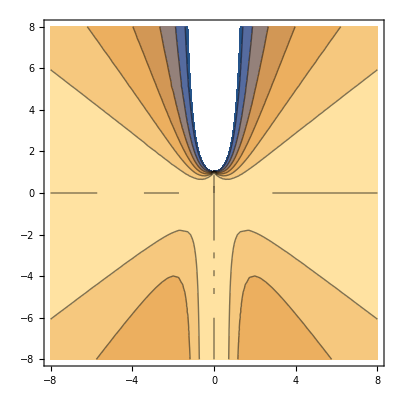

```mathematica
ContourPlot[(1+x^2+x^4-a √(1+x^2))/(√((1+x^2) (1+x^2+x^4) (x^2+(a-1/(√(1+x^2)))^2))),{x,-8,8},{a,-8,8}]
```

```mathematica
FourierTransform[f[x],x,t]
```

√(2/π) BesselK[0,t Sign[t]]

```mathematica
FourierTransform[Cos[2x],x,t]
```

√(π/2) DiracDelta[-2+t]+√(π/2) DiracDelta[2+t]

```mathematica
LaplaceTransform[Cos[2x],x,t]
```

t/(4+t^2)

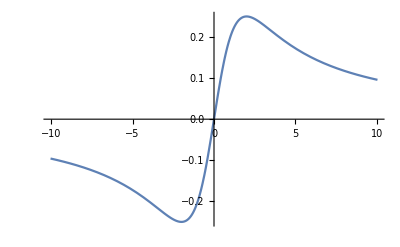

```mathematica
Plot[t/(4+t^2),{t,-10.04,10.04}]
```

```mathematica
SquareWave[x]
```

SquareWave[x]

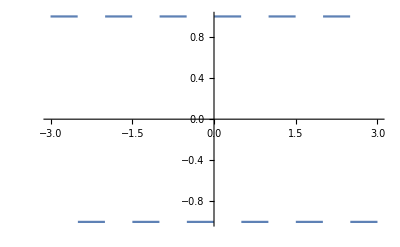

```mathematica
Plot[SquareWave[x],{x,-3,3}]
```

```mathematica
FourierTransform[SquareWave[x],x,t]
```

∑_(K[1]=-∞)^∞ √(2 π) DiracDelta[t+π K[1]] (Piecewise[{{0, K[1]==0}, {-(ⅈ (-1)^K[1] (1+(-1)^K[1]) (-1+ⅈ^K[1])^2)/(2 π K[1]), True}}])

```mathematica
FourierTransform[Sign[x],x,t]
```

(ⅈ √(2/π))/t

```mathematica
FourierTransform[Abs[x],x,t]
```

-(√(2/π))/t^2

```mathematica
LaplaceTransform[Abs[x],x,t]
```

1/t^2

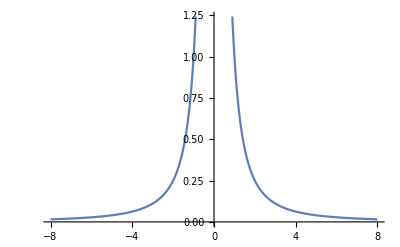

```mathematica
Plot[1/t^2,{t,-8,8}]
```

```mathematica
FourierTransform[DiracDelta[x],x,t]
```

1/(√(2 π))

```mathematica
Square[x]
```

□x

```mathematica
Square
```

Square

```mathematica
FinancialData["SP500","Name"]
```

S&P 500 Index

```mathematica
With[{sp=FinancialData["SP500","Close",All]},
Grid@
TakeLargestBy[
Transpose[{
sp["Dates"][[;;-2]],
Ratios@sp["Values"]
}]
,Last,15]
]
```

Fri 10 Oct 2008 00:00:00GMT-7. | 1.1158
Mon 27 Oct 2008 00:00:00GMT-7. | 1.10789
Tue 20 Oct 1987 00:00:00GMT-7. | 1.09099
Fri 20 Mar 2009 00:00:00GMT-7. | 1.07076
Wed 12 Nov 2008 00:00:00GMT-7. | 1.06921
Fri 21 Nov 2008 00:00:00GMT-7. | 1.06472
Mon 9 Mar 2009 00:00:00GMT-7. | 1.06366
Thu 20 Nov 2008 00:00:00GMT-7. | 1.06325
Tue 23 Jul 2002 00:00:00GMT-7. | 1.05733
Mon 29 Sep 2008 00:00:00GMT-7. | 1.05417
Fri 26 Jul 2002 00:00:00GMT-7. | 1.05408
Mon 19 Oct 1987 00:00:00GMT-7. | 1.05333
Mon 15 Dec 2008 00:00:00GMT-7. | 1.05136
Mon 27 Oct 1997 00:00:00GMT-7. | 1.05115
Fri 4 Sep 1998 00:00:00GMT-7. | 1.0509

```mathematica
With[{sp=FinancialData["SP500","Close",All]},
Grid@
Map[{First@#,PercentForm[Last@#]}&,
TakeSmallestBy[
Transpose[{
sp["Dates"][[;;-2]],
Map[#-1&,Ratios@sp["Values"]]
}]
,Last,15]]
]
```

Fri 16 Oct 1987 00:00:00GMT-7. | -20.47%
Tue 14 Oct 2008 00:00:00GMT-7. | -9.035%
Fri 28 Nov 2008 00:00:00GMT-7. | -8.93%
Fri 26 Sep 2008 00:00:00GMT-7. | -8.807%
Fri 23 Oct 1987 00:00:00GMT-7. | -8.279%
Wed 8 Oct 2008 00:00:00GMT-7. | -7.617%
Fri 24 Oct 1997 00:00:00GMT-7. | -6.866%
Fri 28 Aug 1998 00:00:00GMT-7. | -6.801%
Thu 7 Jan 1988 00:00:00GMT-7. | -6.768%
Wed 19 Nov 2008 00:00:00GMT-7. | -6.712%
Fri 25 May 1962 00:00:00GMT-7. | -6.676%
Fri 5 Aug 2011 00:00:00GMT-7. | -6.663%
Fri 23 Sep 1955 00:00:00GMT-7. | -6.618%
Thu 12 Oct 1989 00:00:00GMT-7. | -6.117%
Tue 18 Nov 2008 00:00:00GMT-7. | -6.116%

```mathematica
Integrate[Exp[-x s],{x,0,∞}]
```

ConditionalExpression[1/s,Re[s]>0]

```mathematica
FullSimplify[Integrate[Exp[-x s],{x,0,∞}],Re[s]>0]
```

1/s

```mathematica
FullSimplify[Integrate[Exp[-x s] f[x],{x,0,∞}],Re[s]>0]
```

1/2 π (-BesselY[0,s]+StruveH[0,s])

```mathematica
BesselY[0,s]
```

BesselY[0,s]

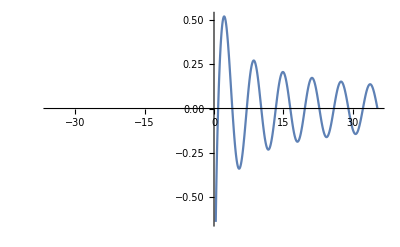

```mathematica
Plot[BesselY[0,s],{s,-35.34645230521432,35.34645230521432}]
```

```mathematica
StruveH[0,s]
```

StruveH[0,s]

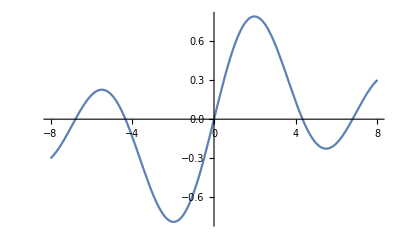

```mathematica
Plot[StruveH[0,s],{s,-8,8}]
```

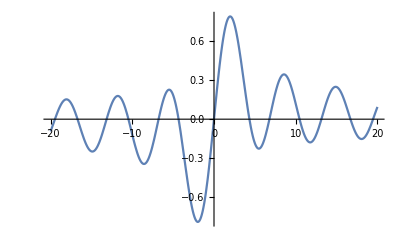

```mathematica
Plot[StruveH[0,s],{s,-20,20}]
```

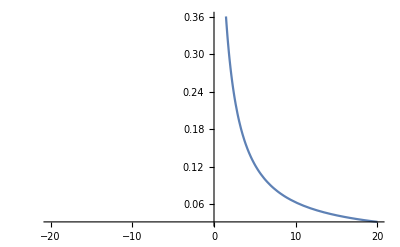

```mathematica
Plot[ (-BesselY[0,s]+StruveH[0,s]),{s,-20,20}]
```

```mathematica
InverseFourierTransform[StruveH[0,s],s,t]
```

(ⅈ √(2/π) (1+UnitStep[-1-t] (-1+UnitStep[t])+(-2+UnitStep[-1+t]) UnitStep[t]))/(√(1-t^2))

```mathematica
FullSimplify[Integrate[Exp[-x s] Sin[2x],{x,0,∞}],Re[s]>0]
```

2/(4+s^2)

```mathematica
HoldAll[FourierTransform[f[x],x,s]]
```

HoldAll[√(2/π) BesselK[0,s Sign[s]]]

```mathematica
f
```

f

```mathematica
HoldAll[FourierTransform[g[x],x,s]]
```

HoldAll[FourierTransform[g[x],x,s]]

```mathematica
FourierTransform[g[x],x,s]
```

FourierTransform[g[x],x,s]

```mathematica
FullForm[FourierTransform[g[x],x,s]]
```

FourierTransform[g[x],x,s]

```mathematica
LaplaceTransform[g[x],x,s]
```

LaplaceTransform[g[x],x,s]

```mathematica
LaplaceTransform[Sin[2 x],x,s]
```

2/(4+s^2)

```mathematica
FourierTransform[Sin[2 x],x,s]
```

ⅈ √(π/2) DiracDelta[-2+s]-ⅈ √(π/2) DiracDelta[2+s]

```mathematica
Integrate[g[x]Exp[2 π ⅈ s],{x,0,∞}]
```

∫_0^∞ ⅇ^(2 ⅈ π s) g[x]ⅆx

```mathematica
Integrate[g[x]Exp[2 π ⅈ s x],{x,0,∞}]
```

∫_0^∞ ⅇ^(2 ⅈ π s x) g[x]ⅆx

```mathematica
Integrate[g[x]Exp[-2 π ⅈ s x],{x,0,∞}]
```

∫_0^∞ ⅇ^(-2 ⅈ π s x) g[x]ⅆx

```mathematica
Integrate[Sin[2x]Exp[-2 π ⅈ s x],{x,0,∞}]
```

ConditionalExpression[1/(2-2 π^2 s^2),Im[s]<0]

```mathematica
Integrate[Sin[2x]Exp[-2 π ⅈ s x],{x,0,∞},Assumptions->Im[s]<0]
```

1/(2-2 π^2 s^2)

```mathematica
Integrate[Sin[2x]Exp[-2 π ⅈ s x],{x,0,∞},Assumptions->Im[s]<0∧Re[s]>0]
```

1/(2-2 π^2 s^2)

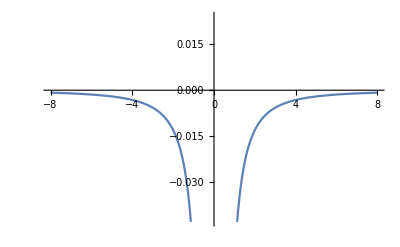

```mathematica
Plot[1/(2-2 π^2 s^2),{s,-8,8}]
```

```mathematica
FourierTransform[Sin[2x],x,s]
```

ⅈ √(π/2) DiracDelta[-2+s]-ⅈ √(π/2) DiracDelta[2+s]

```mathematica
Integrate[Sin[2x]Exp[-2 π ⅈ s x],{x,-∞,∞},Assumptions->Im[s]<0∧Re[s]>0]
```

Integrate[ⅇ^(-2 ⅈ π s x) Sin[2 x],{x,-∞,∞},Assumptions→Im[s]<0&&Re[s]>0]

```mathematica
Integrate[Sin[2x]Exp[-2 π ⅈ s x],{x,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-2 ⅈ π s x) Sin[2 x]ⅆx

```mathematica
Integrate[x Exp[-2 π ⅈ s x],{x,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-2 ⅈ π s x) xⅆx

```mathematica
Integrate[Exp[-2 π ⅈ s x],{x,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-2 ⅈ π s x)ⅆx

```mathematica
FourierTransform[x,x,s]
```

-ⅈ √(2 π) DiracDelta'[s]

```mathematica
FourierTransform[1,x,s]
```

√(2 π) DiracDelta[s]

```mathematica
FourierTransform[g[x],x,s]
```

FourierTransform[g[x],x,s]

```mathematica
FourierTransform[g[s],x,s]
```

FourierTransform[g[s],x,s]

```mathematica
FourierTransform[Sign[x],x,s]
```

(ⅈ √(2/π))/s

```mathematica
FourierTransform[√(1-x^2),x,s]
```

(√(π/2) HankelH1[1,Abs[s]])/Abs[s]

```mathematica
Plot[(√(π/2) HankelH1[1,Abs[s]])/Abs[s],{x,-2,2}]
```

-Graphics-

```mathematica
HankelH1[1,Abs[s]]
```

HankelH1[1,Abs[s]]

```mathematica
HankelH1[1,Abs[x]]
```

HankelH1[1,Abs[x]]

```mathematica
Plot[HankelH1[1,Abs[x]],{x,-2,2}]
```

-Graphics-

```mathematica
Plot[HankelH1[0,x],{x,-2,2}]
```

-Graphics-

```mathematica
FourierTransform[1,x,s]
```

√(2 π) DiracDelta[s]

```mathematica
PowerExpand[√(2 π) DiracDelta[s]]
```

√(2 π) DiracDelta[s]

```mathematica
Integrate[(x^3-x)x,x]
```

-x^3/3+x^5/5

```mathematica
Integrate[(x^3-x)x,{x,-∞,∞}]
```

∫_(-∞)^∞ x (-x+x^3)ⅆx

```mathematica
FullSimplify[Normalize[D[{x,(x^3-x)},x]].Normalize[D[{x,-x},x]],x∈Reals]
```

(2-3 x^2)/(√2 √(1+(1-3 x^2)^2))

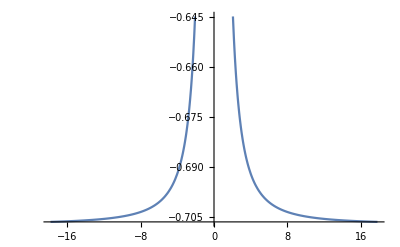

```mathematica
Plot[(2-3 x^2)/(√2 √(1+(1-3 x^2)^2)),{x,-17.832285327461534,17.832285327461534}]
```

```mathematica
Integrate[(t^3-t)(x-t),{t,-∞,∞}]
```

∫_(-∞)^∞ (-t+t^3) (-t+x)ⅆt

```mathematica
Integrate[(t^3-t)(x-t),t]
```

t^3/3-t^5/5-(t^2 x)/2+(t^4 x)/4

```mathematica
Plot3D[t^3/3-t^5/5-(t^2 x)/2+(t^4 x)/4,{t,-8,8},{x,-8,8}]
```

-Graphics3D-

```mathematica
ArcLength[{x,x^2},{x,0,1}]
```

1/4 (2 √5+ArcSinh[2])

```mathematica
Integrate[√2 g[x],{x,0,1}]
```

∫_0^1 √2 g[x]ⅆx

```mathematica
Integrate[√2 g'[x],{x,0,1}]
```

∫_0^1 √2 g'[x]ⅆx

```mathematica
√2(g[1]-g[0])
```

√2 (-g[0]+g[1])

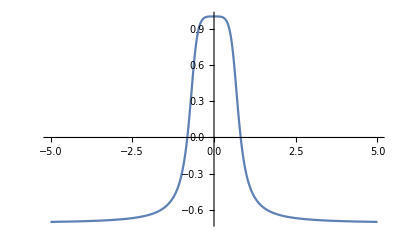

```mathematica
Plot[(2-3 x^2)/(√2 √(1+(1-3 x^2)^2)),{x,-5,5},PlotRange->Full]
```

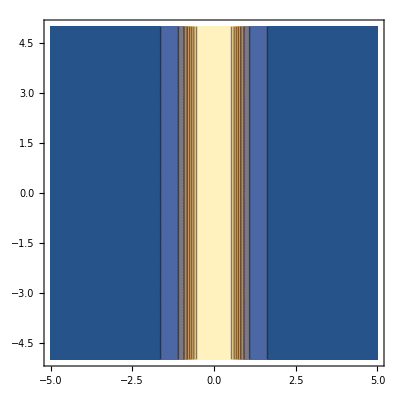

```mathematica
ContourPlot[(2-3 x^2)/(√2 √(1+(1-3 x^2)^2)),{x,-5,5},{y,-5,5}]
```

```mathematica
ContourPlot[(2-3 x^2)/(√2 √(1+(1-3 x^2)^2))==1,{x,-5,5},{y,-5,5}]
```

-Graphics-

```mathematica
(2-3 x^2)/(√2 √(1+(1-3 x^2)^2))==1
```

(2-3 x^2)/(√2 √(1+(1-3 x^2)^2))==1

```mathematica
Reduce[(2-3 x^2)/(√2 √(1+(1-3 x^2)^2))==1]
```

x==0

```mathematica
D[(2-3 x^2)/(√2 √(1+(1-3 x^2)^2)),x]
```

(3 √2 x (1-3 x^2) (2-3 x^2))/((1+(1-3 x^2)^2)^(3/2))-(3 √2 x)/(√(1+(1-3 x^2)^2))

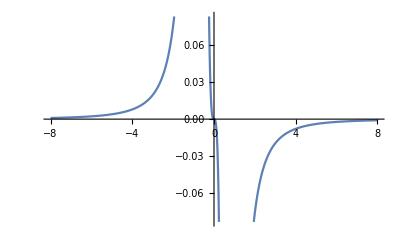

```mathematica
Plot[(3 √2 x (1-3 x^2) (2-3 x^2))/((1+(1-3 x^2)^2)^(3/2))-(3 √2 x)/(√(1+(1-3 x^2)^2)),{x,-8,8}]
```

```mathematica
With[{g=√(1+y'[t]^2)},
D[g,y'[t]]-D[D[g,y[t]],t]==0
]
```

y'[t]/(√(1+y'[t]^2))==0

```mathematica
DSolve[y'[t]/(√(1+y'[t]^2))==0,{y[t]},{t}]
```

{{y[t]→C[1]}}

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
VariationalD[Sqrt[1+y'[x]^2],y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
With[{g=√(1+y'[t]^2)},
D[g,y[t]]-D[D[g,y'[t]],t]==0
]
```

(y'[t]^2 y''[t])/((1+y'[t]^2)^(3/2))-y''[t]/(√(1+y'[t]^2))==0

```mathematica
DSolve[(y'[t]^2 y''[t])/((1+y'[t]^2)^(3/2))-y''[t]/(√(1+y'[t]^2))==0,{y[t],y[t]},{t}]
```

{{y[t]→C[1]+t C[2]}}

```mathematica
VariationalMethods`EulerEquations[Sqrt[1+y'[x]^2],y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
LaplaceTransform[g'[x]==g[x]x,x,s]
```

-g[0]+s LaplaceTransform[g[x],x,s]==LaplaceTransform[x g[x],x,s]

```mathematica
LaplaceTransform[g'[x]==g[x],x,s]
```

-g[0]+s LaplaceTransform[g[x],x,s]==LaplaceTransform[g[x],x,s]

```mathematica
FourierTransform[g'[x]==g[x],x,s]
```

FourierTransform[g'[x]==g[x],x,s]

```mathematica
CloudPut[1]
```

CloudObject[https://www.wolframcloud.com/obj/f1cdbde8-49a4-4eb9-8334-5fb972209783]

```mathematica
Options[obj,Permissions]
```

Options::optnf: Permissions is not a known option for obj.

{}

```mathematica
obj=CloudPut[1]
```

CloudObject[https://www.wolframcloud.com/obj/d73cea19-6e5e-4daf-9fa8-70a4c28d2c16]

```mathematica
Options[obj,Permissions]
```

{Permissions→{Owner→{Read,Write,Execute}}}

```mathematica
SetPermissions[obj,"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

```mathematica
CloudDeploy[Plot[x,{x,-2,2}]]
```

CloudObject[https://www.wolframcloud.com/obj/25402323-058e-4009-a44a-ddd4ec47225a]

```mathematica
SetOptions[CloudObject["https://www.wolframcloud.com/obj/25402323-058e-4009-a44a-ddd4ec47225a"],Permissions->"Public"]
```

{Permissions→Public}

```mathematica
FullSimplify[Normalize[{x,x^2}],x∈Reals]
```

{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}

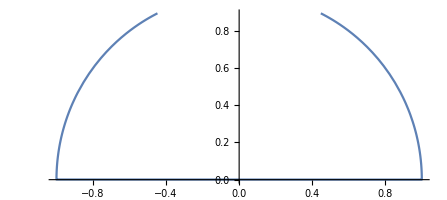

```mathematica
ParametricPlot[{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))},{x,-2,2}]
```

```mathematica
Manipulate[
ParametricPlot[
{{x,x^2},{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}}
,{x,-a,a}]
,{a,.1,5}]
```

```mathematica
Manipulate[
ParametricPlot[
{{x,x^2},{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}}
,{x,-a,a}
,PlotRange->{{-4,4},{-4,4}}]
,{a,.1,5}]
```

```mathematica
CloudDeploy@
Manipulate[
ParametricPlot[
{{x,x^2},{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}}
,{x,-a,a}
,PlotRange->{{-4,4},{-4,4}}]
,{a,.1,5}]
```

CloudObject[https://www.wolframcloud.com/obj/88789a6b-7945-439f-8800-203ff3581a19]

```mathematica
SetOptions[CloudObject["https://www.wolframcloud.com/obj/88789a6b-7945-439f-8800-203ff3581a19"],Permissions->"Public"]
```

{Permissions→Public}